```mathematica
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","Polynomial","TestSuite"}]];
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];
$MaxExtraPrecision=1000;
(*Worland package setup*)
pkgroot=FileNameJoin[Flatten[{quiccroot,"Components","TestSuite","Mathematica"}]];
AppendTo[$Path, pkgroot];
Bessel`$mpprec=100;
Needs["Bessel`"]
ParallelNeeds["Bessel`"]
datadir={"_data","Polynomial","Bessel"};
refdir={"_refdata","Polynomial","Bessel"};

dealiasPolyGrid[n_,l_]:=Floor[3(n+l/2+8)/2];

dealiasGrid[n_,l_]:=Floor[15(2n+l+1)/8];
(*
Configure which output to generate
*)
genRefDataDefault=False;
generateRefData=genRefDataDefault;
configureGenerator[genRef_:genRefDataDefault]:=
Module[{},
generateRefData=genRef;
];
(*
Metadata format
*)
createMetadata[nN_, gridN_,l_]:=Module[{descr,header },
header={
"# Format description",
"# line 1: number of lines",
"# line 2: radial modes", 
"# line 3: radial grid points", 
"# line 4: harmonic degree l" 
};
descr = Flatten[{nN,gridN,l}];
descr = Prepend[descr,Length@descr];
descr = Flatten[Prepend[descr,header]];
descr
];

(*defaultSetup[]:={128,256,{1,2,5,20,128}}*)
defaultSetup[]:={16,32,{0,1,2,5,20,32}}
defaultNoZeroSetup[]:={16,32,{1,2,5,10,20,32}}
```

```mathematica
(*Check basic setup*)
ng=20;
rg = bgrid[ng];
wg=bweights[ng];
(*Table[N[Table[Dot[ValueSphJnl[i,l,rg],wg ValueSphJnl[j,l,rg]],{i,0,5},{j,0,5}],5]//MatrixForm,{l,0,5}]

Table[N[Table[Dot[InsulatingSphJnl[i,l,rg],wg InsulatingSphJnl[j,l,rg]],{i,0,5},{j,0,5}],5]//MatrixForm,{l,0,5}]

Table[N[Table[Dot[StressFreeSphJnl[i,l,rg],wg StressFreeSphJnl[j,l,rg]],{i,0,5},{j,0,5}],5]//MatrixForm,{l,0,5}]*)

Table[N[Table[Dot[NoSlipSphJnl[i,l,rg],wg NoSlipSphJnl[j,l,rg]],{i,0,5},{j,0,5}],5]//MatrixForm,{l,0,5}]
Clear[ng, rg, wg]
```

```mathematica
refop[ns_,gfunc_,wfunc_,opfunc_,name_]:= Module[{outprec = 32,i,maxN,gridN,l, grid,weights, op,msg,descr,tempmsg,fname},
For[i = 1, i≤ Length[ns],i++,
maxN=ns[[i,1]];
gridN = ns[[i,2]];
l=ns[[i,3]];
msg="Exporting "<>name<>" Bessel operator for N = "<>ToString[maxN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[l]<>"...";
tempmsg=PrintTemporary[msg];
(* Generate metadata *)
fname=name<>"_id"<>ToString[i-1]<>"_meta.dat";
descr = createMetadata[maxN,gridN,l];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
fname="weighted_"<>fname;
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate operator *)
If[generateRefData,
grid = gfunc[gridN];
weights=wfunc[gridN];
op=Transpose[Table[opfunc[n,l,grid],{n,0,maxN}]];
op = N[op,outprec];
fname=name<>"_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],op];
fname="weighted_"<>fname;
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],weights*op];
NotebookDelete[tempmsg];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
];
]
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueSphJnl,"Value_SphJnl"];
refop[tests,bgrid,bweights,InsulatingSphJnl,"Insulating_SphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipSphJnl,"NoSlip_SphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueRSphJnl,"Value_rSphJnl"];
refop[tests,bgrid,bweights,InsulatingRSphJnl,"Insulating_rSphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipRSphJnl,"NoSlip_rSphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueDivrSphJnl,"Value_r_1SphJnl"];
refop[tests,bgrid,bweights,InsulatingDivrSphJnl,"Insulating_r_1SphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipDivrSphJnl,"NoSlip_r_1SphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueDSphJnl,"Value_dSphJnl"];
refop[tests,bgrid,bweights,InsulatingDSphJnl,"Insulating_dSphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipDSphJnl,"NoSlip_dSphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueD2SphJnl,"Value_d2SphJnl"];
refop[tests,bgrid,bweights,InsulatingD2SphJnl,"Insulating_d2SphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipD2SphJnl,"NoSlip_d2SphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueSlaplSphJnl,"Value_slaplSphJnl"];
refop[tests,bgrid,bweights,InsulatingSlaplSphJnl,"Insulating_slaplSphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipSlaplSphJnl,"NoSlip_slaplSphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
(*
maxN=128;
maxL=256;
ls ={0,1,2,5,20,128}; 
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,wgrid,wweights,divrWnl,"r_1Wnl_recurrence_t"];
configureGenerator[True];
refop[tests,wgrid,wweights,divrWnl,"r_1Wnl_explicit_t"];
configureGenerator[True];
refop[tests,wgrid,wweights,divrWnl,"r_1Wnl_implicit_t"];
Clear[maxN,maxL,gridN,tests];*)
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN=2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refop[tests,bgrid,bweights,ValueDrSphJnl,"Value_drSphJnl"];
refop[tests,bgrid,bweights,InsulatingDrSphJnl,"Insulating_drSphJnl"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN=2maxN;
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refop[tests,bgrid,bweights,NoSlipDrSphJnl,"NoSlip_drSphJnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,ls}]
(*refop[tests,bgrid,bweights,ValueDivrdrSphJnl,"Value_r_1drSphJnl_recurrence_t"];
refop[tests,bgrid,bweights,InsulatingDivrdrSphJnl,"Insulating_r_1drSphJnl_recurrence_t"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,ls}]
refop[tests,bgrid,bweights,NoSlipDivrdrSphJnl,"NoSlip_r_1drSphJnl_recurrence_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,ls}]
(*refop[tests,bgrid,bweights,ValueRaiseSphJnl,"Value_raiseSphJnl"];
refop[tests,bgrid,bweights,InsulatingRaiseSphJnl,"Insulating_raiseSphJnl"];*)
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,ls}]
(*refop[tests,bgrid,bweights,ValueLowerSphJnl,"Value_lowerSphJnl"];
refop[tests,bgrid,bweights,InsulatingLowerSphJnl,"Insulating_lowerSphJnl"];*)
Clear[maxN,maxL,gridN,tests];
```

```mathematica
refDenseOp[ns_,gfunc_,wfunc_,opfunc_,name_]:= Module[{outprec = 32,i,maxN,gridN,l, grid,weights, op,msg,descr,tempmsg,fbase,fname},
For[i = 1, i≤ Length[ns],i++,
maxN=ns[[i,1]];
gridN = ns[[i,2]];
l=ns[[i,3]];
fbase="weighted_"<>name;
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[maxN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[l]<>"...";
tempmsg=PrintTemporary[msg];
(* Generate metadata *)
fname=fbase<>"_id"<>ToString[i-1]<>"_meta.dat";
descr = createMetadata[maxN,gridN,l];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate operator *)
If[generateRefData,
grid = gfunc[gridN];
weights=wfunc[gridN];
op = opfunc[maxN,l,grid,weights];
op = N[op,outprec];
fname=fbase<>"_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],op];
NotebookDelete[tempmsg];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
];
]
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
configureGenerator[True];
gridN= dealiasGrid[maxN,maxL];
tests=Table[{maxN,gridN,l},{l,ls}]
(*refDenseOp[tests,bgrid,bweights,ValueDivrdrSphJnlExplicit,"Value_r_1drSphJnl_explicit_t"];
refDenseOp[tests,bgrid,bweights,InsulatingDivrdrSphJnlExplicit,"Insulating_r_1drSphJnl_explicit_t"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
configureGenerator[True];
gridN= dealiasGrid[maxN,maxL];
tests=Table[{maxN,gridN,l},{l,ls}]
refDenseOp[tests,bgrid,bweights,NoSlipDivrdrSphJnlExplicit,"NoSlip_r_1drSphJnl_explicit_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
{maxN,maxL,ls}=defaultSetup[];
gridN= dealiasGrid[maxN,maxL];
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
(*refDenseOp[tests,bgrid,bweights,ValueDivrdrSphJnlImplicit,"Value_r_1drSphJnl_implicit_t"];
refDenseOp[tests,bgrid,bweights,InsulatingDivrdrSphJnlImplicit,"Insulating_r_1drSphJnl_implicit_t"];*)
{maxN,maxL,ls}=defaultNoZeroSetup[];
gridN= dealiasGrid[maxN,maxL];
tests=Table[{maxN,gridN,l},{l,ls}]
configureGenerator[True];
refDenseOp[tests,bgrid,bweights,NoSlipDivrdrSphJnlImplicit,"NoSlip_r_1drSphJnl_implicit_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
data=Import["/mnt/data/phmarti/QuICC/build/QuICC_inviscid/mpi/Models/BoussinesqSphereRTC/TestSuite/Benchmarks/BesselBenchmark/wState/profile.dat","Data"];
dataHR=Import["/mnt/data/phmarti/QuICC/build/QuICC_inviscid/mpi/Models/BoussinesqSphereRTC/TestSuite/Benchmarks/BesselBenchmark/wState/profile_hr.dat","Data"];
dataGood=Import["/mnt/data/phmarti/QuICC/build/QuICC_inviscid/mpi/Models/BoussinesqSphereRTC/TestSuite/Benchmarks/BesselBenchmark/wState/profile_good.dat","Data"];
```

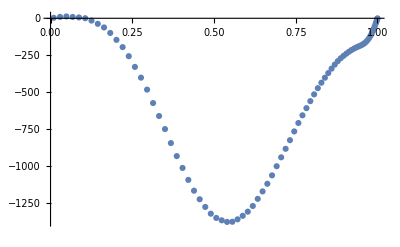

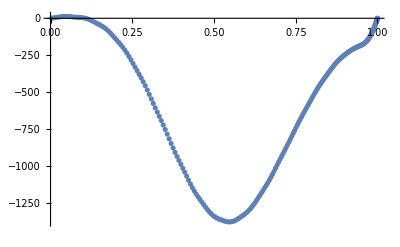

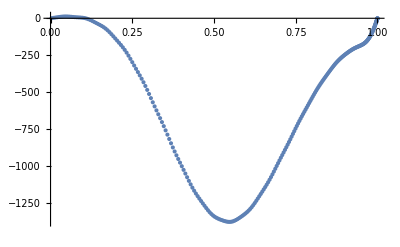

```mathematica
ListPlot[data]
ListPlot[dataHR]
ListPlot[dataGood]
```

```mathematica
db = dataGood;
ng=Dimensions[db][[1]];
rg = bgrid[ng];
wg=bweights[ng];
```

43.8551

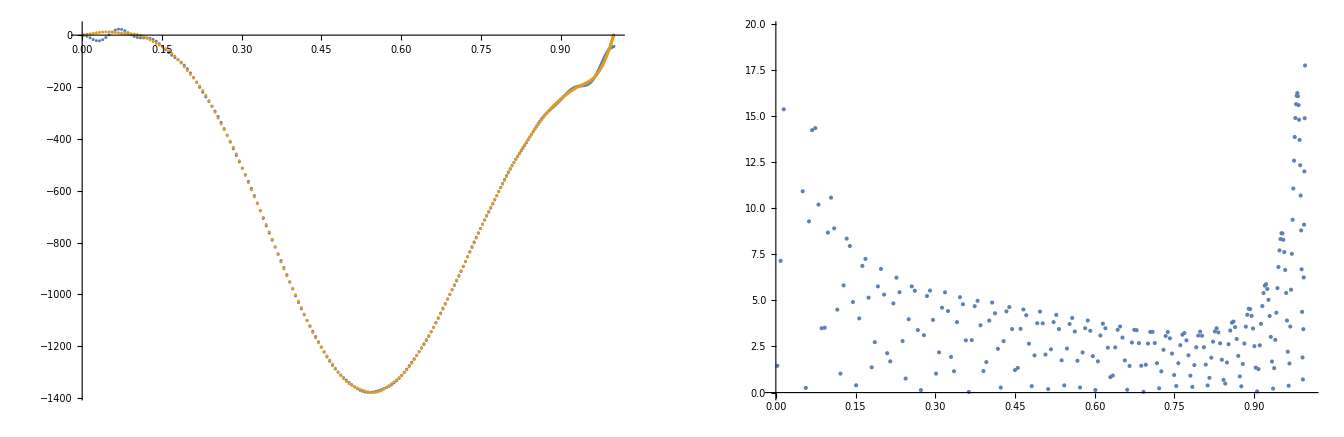

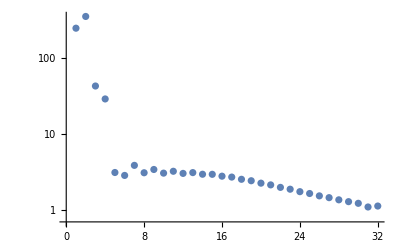

```mathematica
l=2;
maxN=31;
op = Table[NoSlipSphJnl[j,l,rg],{j,0,maxN}]//Transpose;
spec=Transpose[op].DiagonalMatrix[wg].db[[;;,2]];
phys = op.spec;
physErr=Abs[phys-db[[;;,2]]];
Max[physErr]
GraphicsGrid[{{ListPlot[{Transpose[{rg,phys}],db}],ListPlot[Transpose[{rg,physErr}]]}}]
GraphicsGrid[{{ListLogPlot[Abs@spec]}}]
Clear[l,maxN]
```

51.4242

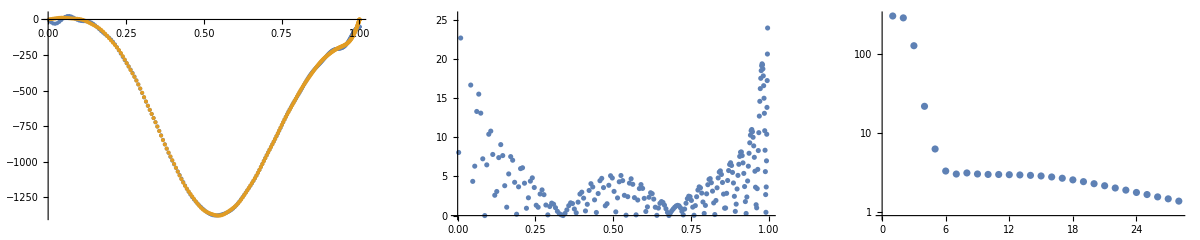

```mathematica
l=1;
maxN=27;
op = Table[NoSlipSphJnl[j,l,rg],{j,0,maxN}]//Transpose;
spec=Transpose[op].DiagonalMatrix[wg].db[[;;,2]];
phys = op.spec;
physErr=Abs[phys-db[[;;,2]]];
Max[physErr]
GraphicsGrid[{{ListPlot[{Transpose[{rg,phys}],db}],ListPlot[Transpose[{rg,physErr}]],ListLogPlot[Abs@spec]}}]
Clear[l,maxN]
```

49.6909

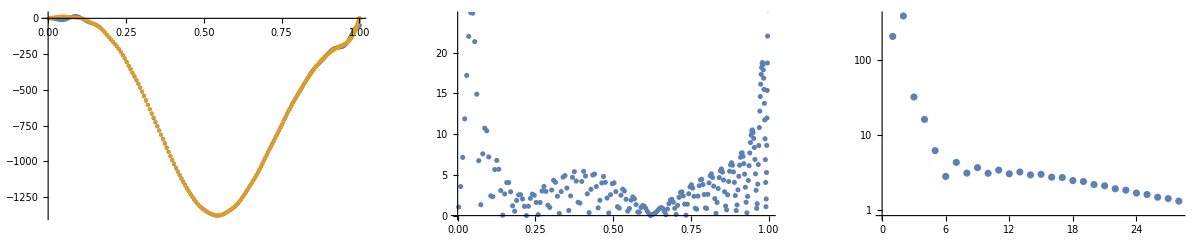

```mathematica
l=3;
maxN=27;
op = Table[NoSlipSphJnl[j,l,rg],{j,0,maxN}]//Transpose;
spec=Transpose[op].DiagonalMatrix[wg].db[[;;,2]];
phys = op.spec;
physErr=Abs[phys-db[[;;,2]]];
Max[physErr]
GraphicsGrid[{{ListPlot[{Transpose[{rg,phys}],db}],ListPlot[Transpose[{rg,physErr}]],ListLogPlot[Abs@spec]}}]
Clear[l,maxN]
```

7.99346

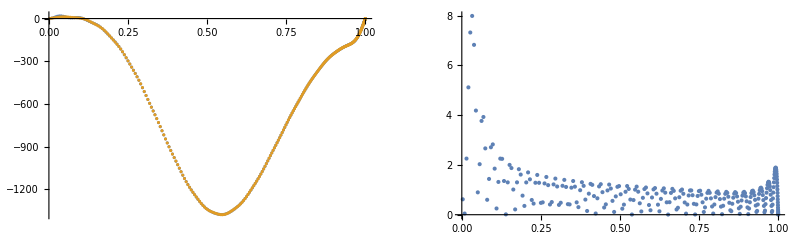

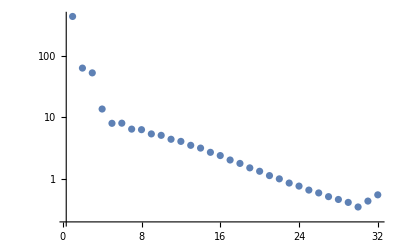

```mathematica
l=2;
maxN=31;
op = Table[ValueSphJnl[j,l,rg],{j,0,maxN}]//Transpose;
spec=Transpose[op].DiagonalMatrix[wg].db[[;;,2]];
phys = op.spec;
physErr=Abs[phys-db[[;;,2]]];
Max[physErr]
GraphicsGrid[{{ListPlot[{Transpose[{rg,phys}],db}],ListPlot[Transpose[{rg,physErr}],PlotRange->All]}}]
GraphicsGrid[{{ListLogPlot[Abs@spec,PlotRange->All]}}]
Clear[l,maxN]
```

0.964519

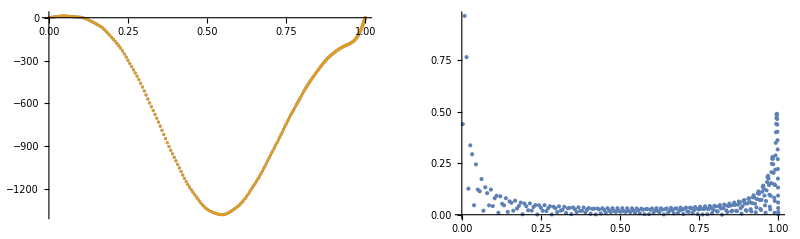

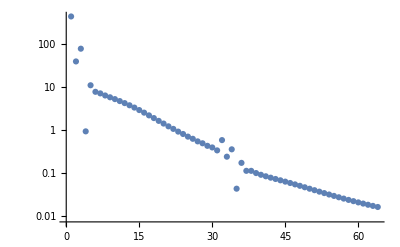

```mathematica
l=1;
maxN=63;
op = Table[ValueSphJnl[j,l,rg],{j,0,maxN}]//Transpose;
spec=Transpose[op].DiagonalMatrix[wg].db[[;;,2]];
phys = op.spec;
physErr=Abs[phys-db[[;;,2]]];
Max[physErr]
GraphicsGrid[{{ListPlot[{Transpose[{rg,phys}],db}],ListPlot[Transpose[{rg,physErr}],PlotRange->All]}}]
GraphicsGrid[{{ListLogPlot[Abs@spec,PlotRange->All]}}]
Clear[l,maxN]
```

4.58019

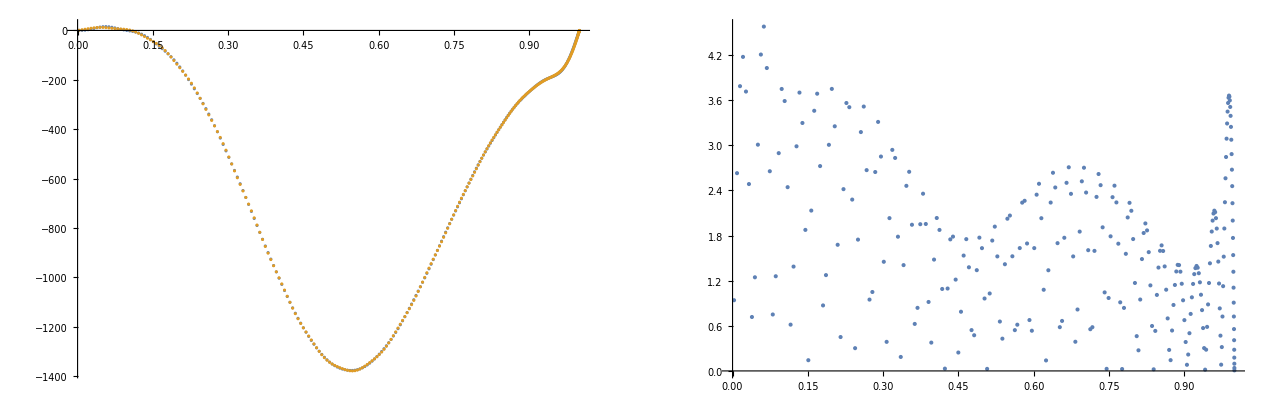

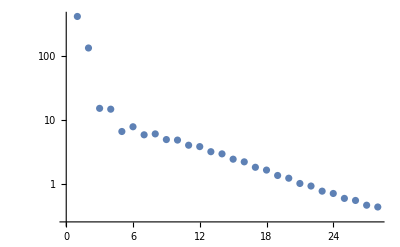

```mathematica
l=3;
maxN=27;
op = Table[ValueSphJnl[j,l,rg],{j,0,maxN}]//Transpose;
spec=Transpose[op].DiagonalMatrix[wg].db[[;;,2]];
phys = op.spec;
physErr=Abs[phys-db[[;;,2]]];
Max[physErr]
GraphicsGrid[{{ListPlot[{Transpose[{rg,phys}],db}],ListPlot[Transpose[{rg,physErr}]]}}]
GraphicsGrid[{{ListLogPlot[Abs@spec]}}]
Clear[l,maxN]
```

```mathematica
(*Check basic setup*)
maxN=9;
ls={1,2,3,5,10,20};
ns={5,7,10,12,15,18,20,22,25,28,30};
err = {};
For[j=1,j<= Length@ls,j++,
errl={};
l=ls[[j]];
For[i =1, i<= Length@ns,i++,
ng=ns[[i]];
rg = bgrid[ng];
wg=bweights[ng];
ortho=Table[Dot[NoSlipSphJnl[i,l,rg],wg NoSlipSphJnl[j,l,rg]],{i,0,maxN},{j,0,maxN}];
(*Print[N[ortho-IdentityMatrix[maxN+1],5]//MatrixForm];*)
AppendTo[errl, ortho[[-1,-1]]-1];
Clear[ng, rg, wg]
];
AppendTo[err,errl];
];
Clear[maxN,l]
```

```mathematica
h[n_]:=SetPrecision[(2^(2n+1)(n!)^4)/((2n+1)((2n)!)^3),100];
```

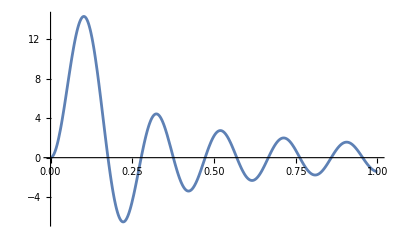

```mathematica
Plot[NoSlipSphJnl[9,2,r],{r,0,1}]
```

```mathematica
h[42]
```

1/20526190243962045235554356879115505787740184806802169012900002049432178446899571237696745017030282811331771936369538182679836432567760457992553710937500

```mathematica
Table[n,{n,1,10,2}]
```

{1,3,5,7,9}

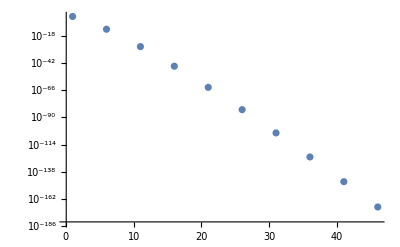

```mathematica
ListLogPlot[Table[{n,h[n]},{n,1,50,5}],PlotRange->All]
```

```mathematica
D[SphericalBesselJ[n,k r],{r,1}]
```

k (-SphericalBesselJ[n,k r]/(2 k r)+1/2 (SphericalBesselJ[-1+n,k r]-SphericalBesselJ[1+n,k r]))

0.00740741

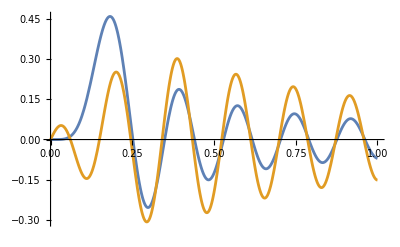

```mathematica
k=2;
n=9;
l=5;
z=nsZero[n,l];
f[r_]:=NoSlipSphJnl[n,l,r]
fk[r_]=D[f[r],{r,2k}];
h[k]//N
Plot[{f[r]/20,fk[r]/(n z^(2k))},{r,0,1},PlotRange->All]
Clear[f,fk,k,z,n,l];
```

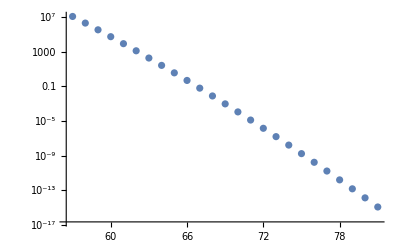

{{57.,1.22371×10^7},{58.,2.10293×10^6},{59.,349188.},{60.,56057.3},{61.,8705.37},{62.,1308.46},{63.,190.449},{64.,26.8573},{65.,3.67135},{66.,0.486717},{67.,0.062606},{68.,0.00781696},{69.,0.000947834},{70.,0.000111656},{71.,0.000012784},{72.,1.42319×10^-6},{73.,1.54111×10^-7},{74.,1.62384×10^-8},{75.,1.66555×10^-9},{76.,1.66352×10^-10},{77.,1.61847×10^-11},{78.,1.53439×10^-12},{79.,1.41798×10^-13},{80.,1.27773×10^-14},{81.,1.12302×10^-15}}

```mathematica
err = {};
nN=29;
l=2;
ngPoly=dealiasGrid[nN,l];
ngNaive=2 (2 nN + l);
ngNaive=81;
ns = Table[n,{n,ngPoly,ngNaive}];
z=nsZero[nN,l];
For[i = 1, i<= Length@ns,i++,
n=ns[[i]];
AppendTo[err,{n,h[n] (nN z^(2n))}];
];
ListLogPlot[Abs@err]
err//N
```

121

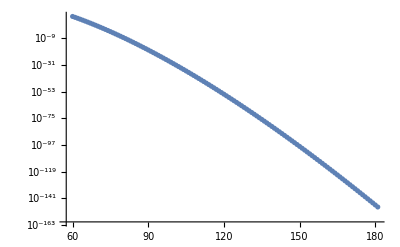

{{60.,7.99519×10^8},{61.,1.45458×10^8},{62.,2.56132×10^7},{63.,4.36753×10^6},{64.,721562.},{65.,115556.},{66.,17947.2},{67.,2704.51},{68.,395.608},{69.,56.197},{70.,7.75564},{71.,1.0403},{72.,0.135676},{73.,0.0172119},{74.,0.00212469},{75.,0.000255306},{76.,0.0000298734},{77.,3.40499×10^-6},{78.,3.78184×10^-7},{79.,4.09439×10^-8},{80.,4.32229×10^-9},{81.,4.45056×10^-10},{82.,4.4712×10^-11},{83.,4.38403×10^-12},{84.,4.19651×10^-13},{85.,3.92277×10^-14},{86.,3.58185×10^-15},{87.,3.19559×10^-16},{88.,2.78638×10^-17},{89.,2.37512×10^-18},{90.,1.9797×10^-19},{91.,1.61394×10^-20},{92.,1.28723×10^-21},{93.,1.00464×10^-22},{94.,7.67444×10^-24},{95.,5.73943×10^-25},{96.,4.20311×10^-26},{97.,3.01473×10^-27},{98.,2.11833×10^-28},{99.,1.45847×10^-29},{100.,9.84128×10^-31},{101.,6.50938×10^-32},{102.,4.22133×10^-33},{103.,2.6845×10^-34},{104.,1.67442×10^-35},{105.,1.02455×10^-36},{106.,6.15107×10^-38},{107.,3.62403×10^-39},{108.,2.09572×10^-40},{109.,1.18974×10^-41},{110.,6.63162×10^-43},{111.,3.63001×10^-44},{112.,1.95159×10^-45},{113.,1.0307×10^-46},{114.,5.34816×10^-48},{115.,2.72693×10^-49},{116.,1.36649×10^-50},{117.,6.73083×10^-52},{118.,3.25928×10^-53},{119.,1.55178×10^-54},{120.,7.26529×10^-56},{121.,3.34544×10^-57},{122.,1.51527×10^-58},{123.,6.75181×10^-60},{124.,2.96008×10^-61},{125.,1.27702×10^-62},{126.,5.42193×10^-64},{127.,2.26585×10^-65},{128.,9.32144×10^-67},{129.,3.77539×10^-68},{130.,1.50564×10^-69},{131.,5.91303×10^-71},{132.,2.28708×10^-72},{133.,8.71335×10^-74},{134.,3.27017×10^-75},{135.,1.20916×10^-76},{136.,4.40533×10^-78},{137.,1.5816×10^-79},{138.,5.59609×10^-81},{139.,1.9516×10^-82},{140.,6.70902×10^-84},{141.,2.27371×10^-85},{142.,7.59732×10^-87},{143.,2.50311×10^-88},{144.,8.13272×10^-90},{145.,2.60597×10^-91},{146.,8.23615×10^-93},{147.,2.56767×10^-94},{148.,7.89689×10^-96},{149.,2.39615×10^-97},{150.,7.17382×10^-99},{151.,2.11937×10^-100},{152.,6.17903×10^-102},{153.,1.77799×10^-103},{154.,5.04975×10^-105},{155.,1.41573×10^-106},{156.,3.91826×10^-108},{157.,1.07065×10^-109},{158.,2.88856×10^-111},{159.,7.69527×10^-113},{160.,2.02448×10^-114},{161.,5.25994×10^-116},{162.,1.34978×10^-117},{163.,3.4213×10^-119},{164.,8.5664×10^-121},{165.,2.11894×10^-122},{166.,5.17822×10^-124},{167.,1.25031×10^-125},{168.,2.98307×10^-127},{169.,7.03309×10^-129},{170.,1.63869×10^-130},{171.,3.7735×10^-132},{172.,8.58857×10^-134},{173.,1.93221×10^-135},{174.,4.29709×10^-137},{175.,9.44734×10^-139},{176.,2.05347×10^-140},{177.,4.41305×10^-142},{178.,9.37754×10^-144},{179.,1.97045×10^-145},{180.,4.09447×10^-147},{181.,8.41415×10^-149}}

```mathematica
err = {};
nN=31;
l=2;
ng=dealiasGrid[nN,l]
ns = Table[n,{n,Floor[ng/2],Floor[3/2 ng]}];
z=valueZero[nN,l];
For[i = 1, i<= Length@ns,i++,
n=ns[[i]];
AppendTo[err,{n,h[n] (nN z^(2n))}];
];
ListLogPlot[Abs@err]
err//N
```

{1,45,3.36610891852084616099762168932871685505273972868313514071641900482073775718290392003813982221388×10^-17}

{4,43,2.29897194905348741861439215378708716396989412663302617501200407845659615118243468880091412109326×10^-18}

{7,42,2.33309886922665529654842929590259911761837986145667957268061013278467875041861689031880574601344×10^-17}

{10,41,2.10521888301060936297380709353678082123333043724057022550870012673239867579715865529797467668429×10^-16}

{13,39,1.07661945630019267381590445293147995638807007737150901321246719736104626033474375153812656901282×10^-17}

{16,38,8.05449317068128343274142588695149345357731364977347527924099949405172842423722546031345930941968×10^-17}

{19,36,3.26489089254856511946772367880266206486600594577687152732702144687467791035938167869132288499699×10^-18}

{22,35,2.02559661730706161426018144045806375073754764674958048902218551346933277884457317355580975817599×10^-17}

{25,34,1.13154237042081663765672472231236237131846150756964307096407156681307695873594597339134537709132×10^-16}

{28,32,3.26695450981329352615060898231878147436589688937746783481362734824741370699953122059926546625623×10^-18}

{31,31,1.51054100087627834177168835704851013831134844925418884913953020312639678244413219821272028706807×10^-17}

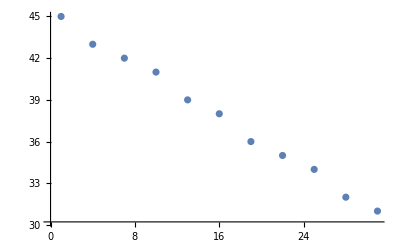

```mathematica
maxL=31;
ngrid=2/3 dealiasGrid[31,maxL];
maxN=ng/2;
ns = Table[n,{n,2,maxN}];
ls = Table[i,{i,1,maxL,3}];
z=nsZero[nN,l];
lmaxN={};
For[j = 1, j<= Length@ls,j++,
l=ls[[j]];
err={};
For[i = 1, i<= Length@ns,i++,
nN=ns[[i]];
z=valueZero[nN,l];
tmpErr=h[ngrid] (nN z^(2ngrid));
AppendTo[err,{nN,tmpErr}];
If[tmpErr>100 $MachineEpsilon,Break[]];
];
maxRes=err[[Length@Select[LessThan[$MachineEpsilon]]@err[[;;,2]]]];
Print[Flatten@{l,maxRes}];
AppendTo[lmaxN,Flatten@{l,maxRes}];
];
err//N;
ListPlot[lmaxN[[;;,{1,2}]]]
```

```mathematica
n=31;
l=31;
dealiasGrid[n,l]//N
dealiasPolyGrid[n,l]
```

176.

81

```mathematica
Floor[3(n+l/2)/2]
```

45